# Model numerical solution

Disclaimer: This notebook was written and revised with assistance from OpenAI Codex. The author remains responsible for verifying all results.

Workflow for the single-resource model, parameter sweeps, and multiple-nutrient extension. Evaluate each section from top to bottom because later cells use definitions created earlier in the same section. This notebook reproduces data used in figure 2.

## 1. Single-resource, multiple-species model

Core notation: S is species richness; n[t] and T[t] are species abundance and local resource vectors; R[t] is the shared resource; alpha is the species nutrient preferences vector; theta and beta are the two parameters scanned below. The first cell clears Global context, so evaluate it before the remaining cells in this section.
This section reproduces data used in figure 2.

### Model setup

```mathematica
ClearAll["Global`*"]
k=1; γ=0.01; Rstar=5;  S=50;
(*Fix the random stream for reproducible species traits*)
SeedRandom[1];
α=RandomReal[{1,5},{1,S}];α=α[[1]];
n[t_]=Table[Symbol["n"<>ToString@i][t],{i,S}];
T[t_]=Table[Symbol["T"<>ToString@i][t],{i,S}];
n0=Table[1,S];
T0=Table[Rstar,S];
incond=Join[Thread[n[0]==n0],Thread[T[0]==T0],{R[0]==Rstar}];
eq=Join[{D[R[t],t]==Rstar - R[t]-β (S R[t] -Total[T[t]]) - γ R[t] (1-θ) Total[Thread[α n[t]]]},Thread[D[n[t],t]==α n[t](θ T[t]+ (1-θ) R[t] )-k n[t]]
,Thread[D[T[t],t]==β (R[t] - T[t]) - α γ θ T[t] n[t]]];
```

### Abundance trajectories for selected theta values

Solve the model at theta = 0, 0.5, and 1 with beta fixed at 1. Sample every species abundance directly from the numerical interpolating functions at regular time intervals, then export one workbook with a separate named tab for each theta value.

```mathematica
(* Sampling and export settings *)
lim=1000;
betaValue=1;
thetaValues={0,0.5,1};
timeStep=1;
sampleTimes=Range[0,lim,timeStep];
headers=Prepend[Table["species_"<>ToString[i],{i,S}],"time"];
(* Solve each theta value and sample all species directly from the interpolating functions *)
abundanceSheets=Table[Module[{solutionRules,abundanceFunctions,abundanceRows},solutionRules=First[Block[{θ=thetaValue,β=betaValue},NDSolve[Join[eq,incond],Join[n[t],T[t],{R[t]}],{t,0,lim}]]];abundanceFunctions=n[t]/. solutionRules;abundanceRows=Table[Prepend[N[abundanceFunctions/. t->sampleTime],sampleTime],{sampleTime,sampleTimes}];"theta="<>ToString[thetaValue,InputForm]->Prepend[abundanceRows,headers]],{thetaValue,thetaValues}];
(* Write one workbook with one named tab per theta value *)
(* Restart Java with enough heap for the large XLSX workbook *)
Needs["JLink`"];
JLink`InstallJava[];
JLink`ReinstallJava[JLink`CommandLine->"java",JLink`JVMArguments->"-Xmx4096m"];
abundanceWorkbook=FileNameJoin[{NotebookDirectory[],"species_abundances_by_theta.xlsx"}];
Export[abundanceWorkbook,"Sheets"->abundanceSheets,"Rules"]
```

/Users/motasem/prime/Work/PhD/projects/spatial structure/figures/final codes and data/fig 2/species_abundances_by_theta.xlsx

### Parametric solver

Build extinction events that clamp a species abundance to zero after it crosses the threshold. ParametricNDSolve then exposes abundance trajectories and the survivor-fraction function for arbitrary theta and beta within the explored domain.

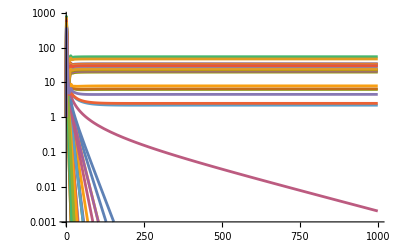

```mathematica
(*parametric*)
lim= 1000;thresh=10^-3;
a=Thread[n[t]<thresh];
b=Thread[n[t]->0];
events=Table[WhenEvent[a[[x]]//Evaluate,b[[x]]//Evaluate],{x,S}];

sol=ParametricNDSolve[Join[eq,incond,events],Join[n[t],T[t],{R[t]}],{t,0,lim},{θ,β}];

func1=n[t]/.sol ;
func2=Through[func1[0.6,1]];
LogPlot[func2,{t,0,lim},PlotRange->{thresh,All}]

survive[θ_,β_]:=Count[Through[func1[θ,β]]/.t->lim,u_/;u>thresh]/S;
```

### Plot the surviving-species fraction over theta on a linear axis and beta on a logarithmic axis.

This  plot  can  be  expensive  because  each  sampled  point  evaluates  the  parametric  numerical  solution .

```mathematica
(*p=DensityPlot[survive[θ,β],{θ,0,1},{β,10^-4,10^4},ScalingFunctions->{"Linear","Log"},PlotLegends->Automatic]*)
```

### Theta sweeps at fixed beta

Create independent theta/beta tasks on the original theta grid from 0 to 1 in steps of 0.05. Evaluate the tasks across available parallel kernels, stop only after a guarded steady-state check, and export one named tab per beta.

```mathematica
(* Configure numerical steady-state checks and define one independent single-resource solve. *)
lim=1000;thresh=1/10^3;steadyStateTolerance=1/10^4;steadyStateMinimumTime=100;steadyStateCheckInterval=25;steadyStateAbundanceSafetyFactor=10;ClearAll[integrationEndTime,singleResourceSurvivalAt];integrationEndTime[solution_List]:=Module[{functions},functions=Head/@solution;Min[(Last[First[#1["Domain"]]]&)/@functions]];singleResourceSurvivalAt[thetaValue_?NumericQ,betaValue_?NumericQ]:=Module[{numericEquations,equationRightSides,stateVector,extinctionConditions,extinctionActions,extinctionEvents,classificationStable,steadyStateCheckTimes,steadyStateEvents,solution,finalTime,finalState,finalAbundances},numericEquations=eq/. {θ->thetaValue,β->betaValue};equationRightSides=Last/@numericEquations;stateVector=Join[n[t],T[t],{R[t]}];extinctionConditions=Thread[n[t]<thresh];extinctionActions=Thread[n[t]->0];extinctionEvents=Table[WhenEvent[Evaluate[Extract[extinctionConditions,speciesIndex]],Evaluate[Extract[extinctionActions,speciesIndex]]],{speciesIndex,S}];classificationStable=And@@(#1==0||#1>=steadyStateAbundanceSafetyFactor thresh&)/@n[t];steadyStateCheckTimes=Range[steadyStateMinimumTime,lim,steadyStateCheckInterval];steadyStateEvents=Table[With[{checkTime=scheduledTime},WhenEvent[Evaluate[t==checkTime&&Max[Abs[equationRightSides]]<steadyStateTolerance&&classificationStable],"StopIntegration"]],{scheduledTime,steadyStateCheckTimes}];solution=NDSolveValue[Join[numericEquations,incond,extinctionEvents,steadyStateEvents],stateVector,{t,0,lim}];finalTime=integrationEndTime[solution];finalState=N[solution/. t->finalTime];finalAbundances=Take[finalState,S];{N[Count[finalAbundances,abundance_/;NumericQ[abundance]&&abundance>thresh]/S],finalTime}];
(* Preserve the current theta grid and the listed fixed-beta cases. *)
thetaSweepGrid=Table[thetaValue,{thetaValue,0,1,0.05}];thetaSweepBetaValues={0.001,0.01,0.1,1,10,100,1000};thetaSweepTasks=Flatten[Table[Association["beta"->betaValue,"theta"->thetaValue],{betaValue,thetaSweepBetaValues},{thetaValue,thetaSweepGrid}],1];
(* Launch available kernels, distribute the model once, and solve parameter pairs concurrently. *)
If[$KernelCount==0,LaunchKernels[]];DistributeDefinitions[integrationEndTime,singleResourceSurvivalAt,eq,incond,n,T,t,S,lim,thresh,steadyStateTolerance,steadyStateMinimumTime,steadyStateCheckInterval,steadyStateAbundanceSafetyFactor];thetaSweepResults=ParallelMap[Function[task,With[{solveResult=singleResourceSurvivalAt[task["theta"],task["beta"]]},Join[task,Association["survivingFraction"->First[solveResult],"stopTime"->Last[solveResult]]]]],thetaSweepTasks,Method->"CoarsestGrained"];
(* Assemble worksheets in the original beta order; stop times remain available in thetaSweepResults. *)
thetaSweepSheets=Table[Module[{sweepRows},sweepRows=({#1["theta"],#1["survivingFraction"]}&)/@Select[thetaSweepResults,#1["beta"]===fixedBeta&];"beta="<>ToString[fixedBeta,InputForm]->Prepend[sweepRows,{"theta","surviving_fraction"}]],{fixedBeta,thetaSweepBetaValues}];thetaSweepWorkbook=FileNameJoin[{NotebookDirectory[],"theta_sweeps_at_fixed_beta.xlsx"}];Export[thetaSweepWorkbook,thetaSweepSheets,"XLSX"];beta001SweepData=Rest["beta=0.001"/. thetaSweepSheets];
```

### Beta sweeps at fixed theta

Preserve the logarithmic beta grid and listed fixed theta values. Evaluate the parameter pairs across available parallel kernels, stop only after a guarded steady-state check, and export one named tab per theta.

```mathematica
(* Configure numerical steady-state checks and define one independent single-resource solve. *)
lim=1000;thresh=1/10^3;steadyStateTolerance=1/10^4;steadyStateMinimumTime=100;steadyStateCheckInterval=25;steadyStateAbundanceSafetyFactor=10;ClearAll[integrationEndTime,singleResourceSurvivalAt];integrationEndTime[solution_List]:=Module[{functions},functions=Head/@solution;Min[(Last[First[#1["Domain"]]]&)/@functions]];singleResourceSurvivalAt[thetaValue_?NumericQ,betaValue_?NumericQ]:=Module[{numericEquations,equationRightSides,stateVector,extinctionConditions,extinctionActions,extinctionEvents,classificationStable,steadyStateCheckTimes,steadyStateEvents,solution,finalTime,finalState,finalAbundances},numericEquations=eq/. {θ->thetaValue,β->betaValue};equationRightSides=Last/@numericEquations;stateVector=Join[n[t],T[t],{R[t]}];extinctionConditions=Thread[n[t]<thresh];extinctionActions=Thread[n[t]->0];extinctionEvents=Table[WhenEvent[Evaluate[Extract[extinctionConditions,speciesIndex]],Evaluate[Extract[extinctionActions,speciesIndex]]],{speciesIndex,S}];classificationStable=And@@(#1==0||#1>=steadyStateAbundanceSafetyFactor thresh&)/@n[t];steadyStateCheckTimes=Range[steadyStateMinimumTime,lim,steadyStateCheckInterval];steadyStateEvents=Table[With[{checkTime=scheduledTime},WhenEvent[Evaluate[t==checkTime&&Max[Abs[equationRightSides]]<steadyStateTolerance&&classificationStable],"StopIntegration"]],{scheduledTime,steadyStateCheckTimes}];solution=NDSolveValue[Join[numericEquations,incond,extinctionEvents,steadyStateEvents],stateVector,{t,0,lim}];finalTime=integrationEndTime[solution];finalState=N[solution/. t->finalTime];finalAbundances=Take[finalState,S];{N[Count[finalAbundances,abundance_/;NumericQ[abundance]&&abundance>thresh]/S],finalTime}];
(* Preserve the original logarithmic beta spacing and listed fixed-theta cases. *)
logspace[a_,b_,numberOfPoints_]:=10.^Range[a,b,(b-a)/(numberOfPoints-1)];betaSweepGrid=logspace[-3,3,50];betaSweepThetaValues={0,0.3,0.5,0.8,1};betaSweepTasks=Flatten[Table[Association["theta"->thetaValue,"beta"->betaValue],{thetaValue,betaSweepThetaValues},{betaValue,betaSweepGrid}],1];
(* Launch available kernels, distribute the model once, and solve parameter pairs concurrently. *)
If[$KernelCount==0,LaunchKernels[]];DistributeDefinitions[integrationEndTime,singleResourceSurvivalAt,eq,incond,n,T,t,S,lim,thresh,steadyStateTolerance,steadyStateMinimumTime,steadyStateCheckInterval,steadyStateAbundanceSafetyFactor];betaSweepResults=ParallelMap[Function[task,With[{solveResult=singleResourceSurvivalAt[task["theta"],task["beta"]]},Join[task,Association["survivingFraction"->First[solveResult],"stopTime"->Last[solveResult]]]]],betaSweepTasks,Method->"CoarsestGrained"];
(* Assemble worksheets in the original theta order; stop times remain available in betaSweepResults. *)
betaSweepSheets=Table[Module[{sweepRows},sweepRows=({#1["beta"],#1["survivingFraction"]}&)/@Select[betaSweepResults,#1["theta"]===fixedTheta&];"theta="<>ToString[fixedTheta,InputForm]->Prepend[sweepRows,{"beta","surviving_fraction"}]],{fixedTheta,betaSweepThetaValues}];betaSweepWorkbook=FileNameJoin[{NotebookDirectory[],"beta_sweeps_at_fixed_theta.xlsx"}];Export[betaSweepWorkbook,betaSweepSheets,"XLSX"];
```

## 2. Two-species susceptibility analysis

This section starts with ClearAll and is independent of Section 1. It uses two nearby alpha values, solves their equilibrium numerically, constructs linear-response coefficients A1 through C3, and defines the susceptibility of species 1 abundance to its mortality perturbation.
This section can be used to reproduce the susceptibility map in figure 3, but it was not used in the paper. The uploaded susceptibility Matlab code was used instead for a faster output.

### Model, equilibrium evaluators, and response coefficients

```mathematica
ClearAll["Global`*"]
k=1; γ=0.01; Rstar=5;  S=2;
α={4.95,5.05};
n[t_]=Table[Symbol["n"<>ToString@i][t],{i,S}];
T[t_]=Table[Symbol["T"<>ToString@i][t],{i,S}];
n0=Table[1,S];
T0=Table[Rstar,S];
incond=Join[Thread[n[0]==n0],Thread[T[0]==T0],{R[0]==Rstar}];
eq=Join[{D[R[t],t]==Rstar - R[t]-β (S R[t] -Total[T[t]]) - γ R[t] (1-θ) Total[Thread[α n[t]]]},Thread[D[n[t],t]==α n[t](θ T[t]+ (1-θ) R[t] )-k n[t]]
,Thread[D[T[t],t]==β (R[t] - T[t]) - α γ θ T[t] n[t]]];

lim= 1000;thresh=10^-3;
a=Thread[n[t]<thresh];
b=Thread[n[t]->0];
events=Table[WhenEvent[a[[x]]//Evaluate,b[[x]]//Evaluate],{x,S}];

sol=ParametricNDSolve[Join[eq,incond,events],Join[n[t],T[t],{R[t]}],{t,0,lim},{θ,β}];

funcN=n[t]/.sol ;
funcR={R[t]/.sol};
funcT=T[t]/.sol ;
Neval[θ_,β_]:=Through[funcN[θ,β]]/.t->lim;
Teval[θ_,β_]:=Through[funcT[θ,β]]/.t->lim;
Reval[θ_,β_]:=Through[funcR[θ,β]]/.t->lim;
R[θ_,β_]:=Reval[θ,β][[1]];
T1[θ_,β_]:=Teval[θ,β][[1]];
T2[θ_,β_]:=Teval[θ,β][[2]];
N1[θ_,β_]:=Neval[θ,β][[1]];
N2[θ_,β_]:=Neval[θ,β][[2]];


FullSimplify[Solve[{0==A1 δR + A2 δN1 - δk1,0==B1 δR + B2 δN2 - δk2,0==C1 δR + C2 δN1 + C3 δN2},{δN1,δN2,δR}]];
A1[θ_,β_]:=α[[1]] (1-θ) + (α[[1]] θ β)/(β + α[[1]] γ θ N1[θ,β]);
A2[θ_,β_]:=(-α[[1]]^2 θ^2 γ T1[θ,β])/(β + α[[1]] γ θ N1[θ,β]);
B2[θ_,β_]:=(-α[[2]]^2 θ^2 γ T2[θ,β])/(β + α[[2]] γ θ N2[θ,β]);
B1[θ_,β_]:=α[[2]] (1-θ) + (α[[2]] θ β)/(β + α[[2]] γ θ N2[θ,β]);
C1[θ_,β_]:=-1 - 2 β + β^2/(β + α[[1]] γ θ N1[θ,β])+ β^2/(β + α[[2]] γ θ N2[θ,β])-γ (1-θ) (α[[1]] N1[θ,β] + α[[2]] N2[θ,β]);
C2[θ_,β_]:=-α[[1]] γ (1-θ) R[θ,β] - (α[[1]] γ θ β T1[θ,β])/(β + α[[1]] γ θ N1[θ,β]);
C3[θ_,β_]:=-α[[2]] γ (1-θ) R[θ,β] - (α[[2]] γ θ β T2[θ,β])/(β + α[[2]] γ θ N2[θ,β]);

suscN1k1[θ_,β_]:=(B2[θ,β] C1[θ,β] -B1[θ,β] C3[θ,β])/(A2[θ,β] B2[θ,β] C1[θ,β]-A1[θ,β] B2[θ,β] C2[θ,β]-A2[θ,β] B1[θ,β] C3[θ,β]);
```

### Susceptibility map

Load the Parula-like color function and map log10 of the absolute susceptibility across theta and beta. Internet access is required only for the external color-map import.

```mathematica
(*load matlab colormap*)
Import["https://pastebin.com/raw/uUJ4rmc1","Package"]

(*plot*)
susceptibilityPlot=DensityPlot[Log10[Abs[suscN1k1[θ,β]]],{θ,0.05,0.95},{β,10^-4,10^4},ScalingFunctions->{"Linear","Log"},PlotLegends->Automatic,ColorFunction->parulaNew,PlotRange->Full]
```

#### Optional SVG export

Export the named susceptibility figure as SVG.

```mathematica
Export["susceptibility.svg",susceptibilityPlot,"SVG"]
```

#### Spot checks

Evaluate susceptibility at two representative parameter combinations to inspect the plotted numerical range.

```mathematica
Log10[Abs[suscN1k1[0.95,1]]]
Log10[Abs[suscN1k1[0.05,10^4]]]
```